# Practical 3 (Newton-Raphson Method)

## Q1. Find approximate root of the equation x^4- x - 10 =0 Solution:

1th iteration's value is: 1.87097

Estimated error is: 0.129032

2th iteration's value is: 1.85578

Estimated error is: 0.015187

3th iteration's value is: 1.85558

Estimated error is: 0.000196141

Return[1.85558]

Final approximate root is: 1.85558

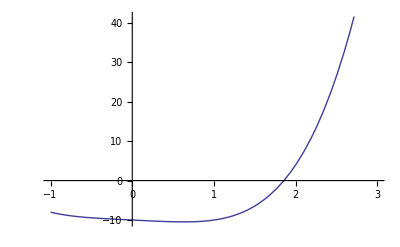

```mathematica
f[x_]:= x^4 - x - 10
Subscript[x, 0]=2;
e= 5*10^-5;
iterations=5;
For[n=1,n≤iterations,n++,
Subscript[x, n]= N[Subscript[x, n-1]- f[Subscript[x, n-1]]/f'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e,Return[Subscript[x, n]]];
Print[n,"th iteration's value is: ",Subscript[x, n]];
Print["Estimated error is: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["Final approximate root is: ",Subscript[x, n]]
Plot[f[x],{x,-1,3}]
```

## Q2. Find the approximate root of the following: i) 3x - Cos(x) - 1 ii) Cosx - xe^x=0 iii)e^-x=x Solution: i)3x - Cos(x) - 1

1th iteration's value is: 0.620016

Estimated error is: 0.379984

2th iteration's value is: 0.607121

Estimated error is: 0.0128953

Return[0.607102]

Final approximate root is: 0.607102

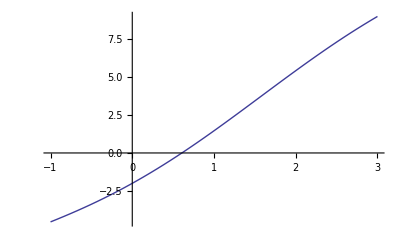

```mathematica
f[x_]:= 3x - Cos[x]-1
Subscript[x, 0]=1;
e= 5*10^-5;
iterations=5;
For[n=1,n≤iterations,n++,
Subscript[x, n]= N[Subscript[x, n-1]- f[Subscript[x, n-1]]/f'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e,Return[Subscript[x, n]]];
Print[n,"th iteration's value is: ",Subscript[x, n]];
Print["Estimated error is: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["Final approximate root is: ",Subscript[x, n]]
Plot[f[x],{x,-1,3}]
```

## Solution: ii)Cosx - xe^x=0

1th iteration's value is: 0.653079

Estimated error is: 0.346921

2th iteration's value is: 0.531343

Estimated error is: 0.121736

3th iteration's value is: 0.51791

Estimated error is: 0.0134335

4th iteration's value is: 0.517757

Estimated error is: 0.00015253

Return[0.517757]

Final approximate root is: 0.517757

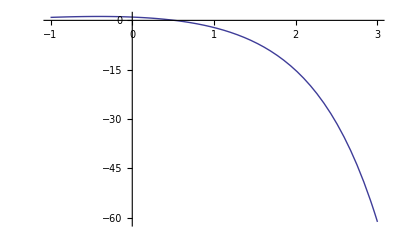

```mathematica
g[x_]:= Cos[x]-x*ⅇ^x
Subscript[x, 0]=1;
err= 5*10^-5;
iterations=5;
For[n=1,n≤iterations,n++,
Subscript[x, n]= N[Subscript[x, n-1]- g[Subscript[x, n-1]]/g'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<err,Return[Subscript[x, n]]];
Print[n,"th iteration's value is: ",Subscript[x, n]];
Print["Estimated error is: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["Final approximate root is: ",Subscript[x, n]]
Plot[g[x],{x,-1,3}]
```

## iii) e^-x=x Solution:

1th iteration's value is: 0.537883

Estimated error is: 0.462117

2th iteration's value is: 0.566987

Estimated error is: 0.0291041

3th iteration's value is: 0.567143

Estimated error is: 0.000156295

Return[0.567143]

Final approximate root is: 0.567143

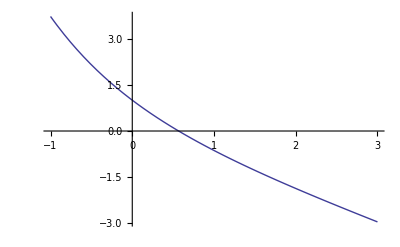

```mathematica
g[x_]:= ⅇ^-x-x
Subscript[x, 0]=1;
err= 5*10^-5;
iterations=5;
For[n=1,n≤iterations,n++,
Subscript[x, n]= N[Subscript[x, n-1]- g[Subscript[x, n-1]]/g'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<err,Return[Subscript[x, n]]];
Print[n,"th iteration's value is: ",Subscript[x, n]];
Print["Estimated error is: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["Final approximate root is: ",Subscript[x, n]]
Plot[g[x],{x,-1,3}]
```